## ϕ Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
phi=RealDigits[GoldenRatio,10,10000][[1,2;;]];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[phi]
```

{0.192807,0.94922}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[phi];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→2,11→180,2→2339,4→1513,14→110,12→156,10→208,15→78,31→6,3→2147,8→377,7→495,5→997,6→640,16→64,9→326,21→17,19→39,23→11,27→10,17→51,13→100,18→34,26→14,20→24,24→15,28→5,30→3,32→4,22→12,25→8,29→6,36→1,37→2,38→1,44→1,35→1,42→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

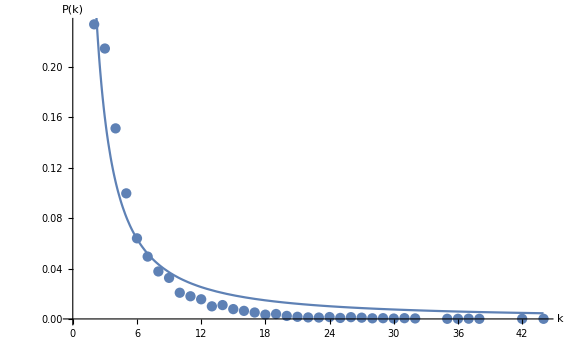
{{C→0.68789,γ→1.32913},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[phi];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→2,5→900,2→3847,4→1342,7→406,9→159,8→246,6→599,3→2311,10→95,14→4,11→52,12→29,13→5,15→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

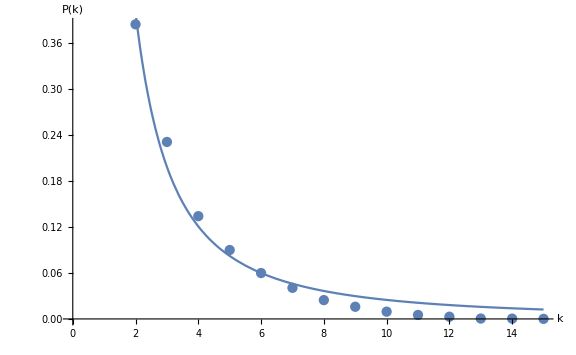
{{C→1.32351,γ→1.72682},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```